```mathematica
SetDirectory["/Users/danikaluntz-martin/Desktop/Advanced Lab/DoubleSlit-ED"];
counts2 = Import["20141122_double_slit_bulb_counts2.csv"];
counts2;
```

```mathematica
θ = (x -x0 )/R;
α = π * a * Sin[θ]/λ;
β = π * d * Sin[θ]/λ; 

Subscript[i, 2] = i0 * (Sinc[α])^2 * Cos[β]^2;
```

```mathematica
x0= 6.3;
a = 0.09;
d = 0.335;
R = 650;
λ = .000546;
```

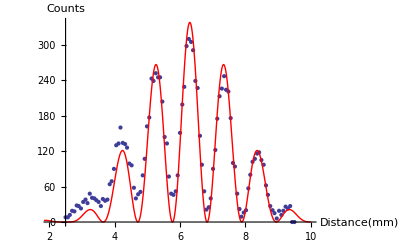

```mathematica
fit2 = NonlinearModelFit[counts2,Subscript[i, 2], i0, x];
Normal[fit2];
plot2 = Plot[fit2[x], {x, -10, 10}, PlotRange->All,PlotStyle->Red];
Show[ListPlot[counts2], plot2, PlotRange-> {{2,10},All},AxesLabel-> {Distance [mm],Counts}]
```

```mathematica
ChiSq2=∑_(j=1)^105 ((fit2["FitResiduals"][[j]])/(2(√counts2[[j,2]]-√1.68)))^2
RedChiSq2 = ChiSq2/7
```

487.614

69.6591